```mathematica
sampleDensity = 10;(*sample density of the trjectory record*)
traceSET=8;
gSET=10;
hSET=7;


yLst={0,0,0,0,1,1,1,1};
mLst={0,1,0,1,0,1,0,1};
aLst={0,0,1,1,0,0,1,1};
fH[hh_,ii_]:=Exp[-hh*((x1-1/2)*(mLst[[ii]]-1/2)+(x2-1/2)*(aLst[[ii]]))];
fD[gg_,ii_]:=Exp[gg*((yLst[[ii]]-mLst[[ii]]*aLst[[ii]])^2-1/2)];
matJumpLST=Transpose[({{-(fH[h,1]*(2+fD[g,1])), fH[h,1], fH[h,1], 0, fH[h,1]*fD[g,1], 0, 0, 0}, {fH[h,2], -(fH[h,2]*(2+fD[g,2])), 0, fH[h,2], 0, fH[h,2]*fD[g,2], 0, 0}, {fH[h,3], 0, -(fH[h,3]*(2+fD[g,3])), fH[h,3], 0, 0, fH[h,3]*fD[g,3], 0}, {0, fH[h,4], fH[h,4], -(fH[h,4]*(2+fD[g,4])), 0, 0, 0, fH[h,4]*fD[g,4]}, {fH[h,5]*fD[g,5], 0, 0, 0, -(fH[h,5]*(2+fD[g,5])), fH[h,5], fH[h,5], 0}, {0, fH[h,6]*fD[g,6], 0, 0, fH[h,6], -(fH[h,6]*(2+fD[g,6])), 0, fH[h,6]}, {0, 0, fH[h,7]*fD[g,7], 0, fH[h,7], 0, -(fH[h,7]*(2+fD[g,7])), fH[h,7]}, {0, 0, 0, fH[h,8]*fD[g,8], 0, fH[h,8], fH[h,8], -(fH[h,8]*(2+fD[g,8]))}})];(*NEQ matrix, EQ matrix*)

timeLST={1,2,3,4,5,6};
signalLST={4,1,4,1,4,1};
periods=Length[timeLST];


trajectoryLST=Table[0,{i,1,sampleDensity*periods}];


(*Propogator*)
fProp[j_,i_,t_,t0_]:=Sum[Exp[eigenVa[[m]]*(t-t0)]*eigenVeR[[m,j]]*eigenVeL[[m,i]],{m,1,8}];
(*Initialize*)
distT={1,0,0,0,0,0,0,0};
```

```mathematica
i=1;

While[i<=periods,
matJump=N[matJumpLST/.{g->gSET,h->hSET,x1->mLst[[signalLST[[i]]]],x2->aLst[[signalLST[[i]]]]}];
eigenVa=Eigenvalues[matJump];(*Transpose[eigenVeL].eigenVeR*) (*verify the orthogonality of left- and right-eigenvectors*)
eigenVeR=Eigenvectors[matJump];
eigenVeL=Eigenvectors[Transpose[matJump]];
eigenVeL=Table[eigenVeL[[i]]/(eigenVeL[[i]].eigenVeR[[i]]),{i,1,8}];
trajectoryLST[[(i-1)*sampleDensity+1;;i*sampleDensity]]=Table[Sum[fProp[traceSET,k,t,0]*distT[[k]],{k,1,8}],{t,1,sampleDensity}];
distTR=Table[Sum[fProp[j,k,i,i-1]*distT[[k]],{k,1,8}],{j,1,8}];
distT=distTR;i++]
```

General::munfl: Exp[-865.609] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

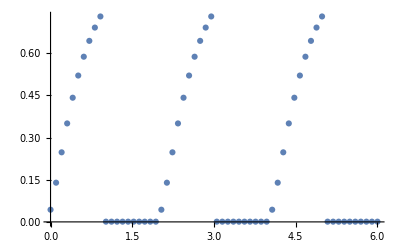

```mathematica
ListPlot[trajectoryLST,DataRange->{0,6}]
```